# Bias control of MCHMC

## Expectation values

```mathematica
R[n_]:= If[n==0, 1, (d+n-2)R[n-2]];  (* = <r^n> *)
Nwick[n_]:= If[n==0, 1,(n-1)Nwick[n-2]]; (* number of Wick's contractions for the n-point correlation function*)
A[n_, m_]:=Nwick[m]R[n+m]/R[m]; (* = <r^n (u.x)^m> *)
rules[order_] := Table[r^(2n) xu^(order-2n)-> A[2n,order-2n] , {n,0,order/2}]; (* insert values for = <r^n (u.x)^m> with n+m = order*)
Drule = {D-> d-1};
Allrules[expr_, order_]:= If[order==0, expr, Allrules[expr/.rules[order], order-2]]/.Drule//Simplify;
```

```mathematica
rules[4]
rules[2]
```

{xu^4→3,r^2 xu^2→2+d,r^4→d (2+d)}

{xu^2→1,r^2→d}

## Euler

### Standard Normal

```mathematica
δ = ϵ r / D;
Energy = D Log[Cosh[δ] - xu Sinh[δ]/r] + ϵ^2 / 2 + ϵ xu;
series = Series[Energy, {ϵ, 0, 2}] //Simplify
```

((D+r^2-xu^2) ϵ^2)/(2 D)+O[ϵ]^3

```mathematica
E1 = Allrules[Expand[ SeriesCoefficient[series, 2] ], 2]
```

1

```mathematica
series = Series[Energy^2, {ϵ, 0, 4}] //Simplify
```

((D+r^2-xu^2)^2 ϵ^4)/(4 D^2)+O[ϵ]^5

```mathematica
E2 = Allrules[Expand[ SeriesCoefficient[series, 4] ], 4]
```

(1-2 d)/(2-2 d)

```mathematica
E2 - E1^2 //Simplify
```

1/(2 (-1+d))

### General Gaussian

```mathematica
δ = ϵ Hx / D;
Energy = D Log[Cosh[δ] - uHx Sinh[δ]/Hx] + ϵ^2 uHu/ 2 + ϵ uHx;
Series[Energy, {ϵ, 0, 3}] //Simplify
```

((Hx^2+D uHu-uHx^2) ϵ^2)/(2 D)+(uHx (Hx^2-uHx^2) ϵ^3)/(3 D^2)+O[ϵ]^4

```mathematica
series = Series[Energy^2, {ϵ, 0, 4}] //Simplify
```

((Hx^2+D uHu-uHx^2)^2 ϵ^4)/(4 D^2)+O[ϵ]^5

```mathematica
Expand[ SeriesCoefficient[series, 4] ]
```

Hx^4/(4 D^2)+(Hx^2 uHu)/(2 D)+uHu^2/4-(Hx^2 uHx^2)/(2 D^2)-(uHu uHx^2)/(2 D)+uHx^4/(4 D^2)

## Leapfrog

### Standard Normal

```mathematica
x1 =Sqrt[r^2 + ((ϵ^2)/ 4) + ϵ xu];
δ = ϵ x1 / D;
x1u = xu +ϵ/2;
b = Sinh[δ] - x1u (Cosh[δ] -1)/x1;
a =  Cosh[δ] - x1u Sinh[δ] / x1;
α = -1+ (1 - ϵ b/(2 x1)) /a;
β = - b/(a  x1);
```

x_ϵ^2

```mathematica
X2 = (r^2(1 + ϵ β/2)^2 +ϵ(2+α)(1 + ϵ β / 2)xu + ((ϵ/2)(2 + α))^2 );
series = Series[X2 , {ϵ, 0, 4}] //Simplify
```

r^2+2 xu ϵ+((D-r^2+xu^2) ϵ^2)/D+((-r^2 xu+xu^3) ϵ^3)/D^2-(((r^2-xu^2) (3 D-2 r^2+6 xu^2)) ϵ^4)/(6 D^3)+O[ϵ]^5

```mathematica
Allrules[Expand[ SeriesCoefficient[series, 2] ], 2]
```

0

```mathematica
Allrules[Expand[ SeriesCoefficient[series, 4] ], 4]
```

1/(6-6 d)

```mathematica
0.6^(1/4)
```

0.880112

```mathematica
Energy
```

```mathematica
Energy = D Log[Cosh[δ] - x1u Sinh[δ]/x1] + (X2 - r^2)/2;
series = Series[Energy, {ϵ, 0, 4}] //Simplify
```

((-r^2 xu+xu^3) ϵ^3)/(6 D^2)-(((r^2-xu^2) (D-r^2+3 xu^2)) ϵ^4)/(12 D^3)+O[ϵ]^5

```mathematica
E1 = Allrules[Expand[SeriesCoefficient[series, 4]], 4]
```

Allrules[0,4]

```mathematica
series = Series[(Energy)^2, {ϵ, 0, 6}] //Simplify
```

((3 D uHHx-3 D uHu uHx-2 uHx^3+2 uHx xHHx)^2 ϵ^6)/(144 D^4)+O[ϵ]^7

```mathematica
Allrules[Expand[SeriesCoefficient[series, 6]], 6]
```

(1+d)/(36 (-1+d)^3)

```mathematica
Sqrt[(0.1^3) / 6]
```

0.0129099

```mathematica
General Gaussian
```

```mathematica
e1e1 = h1^2  + 2 h2;
e2e1 = h1 h2 + 2 h3;
e1e1e1 = h1^3 + 6 h1 h2 + 8 h3;
Feynman = {xHHu^2 -> h3/R[2], 
uHu xHHu xHu -> e2e1/R[4],
uHu^2 xHu^2-> e1e1e1/R[6], 
xHHu xHu^3-> 3 e2e1/R[4], 
xHu^4 uHu -> 3 e1e1e1/R[6],
xHu^6 -> 15 e1e1e1/R[6],
xHHx xHHu xHu -> e2e1/R[2],
xHHx xHu^2 uHu -> (h1 e1e1 + 2 e2e1)/R[4],
xHHx xHu^4 -> 3 e1e1e1/R[4],
xHHx^2 xHu^2 -> e1e1e1/R[2]
};
```

```mathematica
Hx1 =Sqrt[xHHx+ (ϵ^2 / 4) uHHu + ϵ xHHu];
δ = ϵ Hx1 / D;
eu = -(xHu + (ϵ/2)uHu)/Hx1;
b = Sinh[δ] + eu (Cosh[δ] -1);
a =  Cosh[δ] + eu Sinh[δ] ;
α = (ϵ/2)(1+1/a) ;
β = -(ϵ/2)(b/a)/Hx1;
γ = -((ϵ^2)/4)(b/a)/Hx1;
```

```mathematica
X2 = xHx + α^2 uHu + β^2 xHHHx + γ^2 uHHHu + 2 (α xHu + β xHHx + γ xHHu + α β xHHu + α γ uHHu + β γ xHHHu);
Energy = D Log[Cosh[δ] + eu Sinh[δ]] + (X2 - xHx)/2;
series = Series[Energy , {ϵ, 0, 3}] //Simplify
```

((-3 D xHHu+3 D uHu xHu-2 xHHx xHu+2 xHu^3) ϵ^3)/(12 D^2)+O[ϵ]^4

```mathematica
series = Series[Energy ^2, {ϵ, 0, 6}] //Simplify
```

((3 D xHHu-3 D uHu xHu+2 xHHx xHu-2 xHu^3)^2 ϵ^6)/(144 D^4)+O[ϵ]^7

```mathematica
E2 = Expand[SeriesCoefficient[series, 6]]/.Feynman/.{D-> d-1}//Simplify
```

((-17+d) h1^3-6 (-3-2 d+d^2) h1 h2+(32+38 d+33 d^2+9 d^3) h3)/(144 (-1+d)^3 d (2+d) (4+d))

```mathematica
((h1/d)^3-6(h1/d) (h2/d)+9 (h3/d))/(144 d^3)
```

```mathematica
E2 /.{h1 -> d, h2-> d, h3 -> d} //Simplify
```

(1+d)/(36 (-1+d)^3)

```mathematica
Series[xi xj + α^2 ui uj + β^2 HHxi xj + γ^2 HHui uj + 2 (α xi uj + β Hxi xj + (γ + α β) Hxi uj + α γ Hui uj + β γ HHxi uj), {ϵ, 0, 4}] //Simplify
```

xi xj+2 uj xi ϵ+((D ui uj+uj xHu xi-Hxi xj) ϵ^2)/D-((uj (xHHx-2 xHu^2) xi+D uj (3 Hxi-2 ui xHu-uHu xi)+Hxi xHu xj) ϵ^3)/(2 D^2)+1/(12 D^3)(-6 D^2 (Hui-uHu ui) uj-3 D (5 Hxi uj xHu+ui uj (2 xHHx-5 xHu^2)+2 uj xHHu xi-4 uHu uj xHu xi-HHxi xj+Hxi uHu xj)+2 (-5 uj xHHx xHu xi+6 uj xHu^3 xi+2 Hxi xHHx xj-3 Hxi xHu^2 xj)) ϵ^4+O[ϵ]^5

```mathematica
Order0: Sigma_ij
Order1: 0
Order2: 0
```

```mathematica
order 4:
```

```mathematica
epeme1 = (h1 id + 2 H);
rules4 = {xHHu xi uj-> H/R[2],uHu xHu xi uj->epeme1/R[4] ,xHHx xHu xi uj-> epeme1/R[2],xHu^3 xi uj->3 epeme1 / R[4],
Hxi xHHx xj -> epeme1 ,Hxi xHu^2 xj-> epeme1/R[2],
Hxi uj xHu-> H /R[2], ui uj xHu^2-> epeme1 / R[4],   Hxi uHu xj->  h1 id /R[2],
HHxi xj ->  H, Hui uj->  H /R[2] , uHu ui uj -> epeme1/ R[4], ui uj xHHx-> h1 id / R[2]
};
Expand[-6 D^2 (Hui-uHu ui) uj-3 D (5 Hxi uj xHu+ui uj (2 xHHx-5 xHu^2)+2 uj xHHu xi-4 uHu uj xHu xi-HHxi xj+Hxi uHu xj)+2 (-5 uj xHHx xHu xi+6 uj xHu^3 xi+2 Hxi xHHx xj-3 Hxi xHu^2 xj)]
```

-6 D^2 Hui uj+6 D^2 uHu ui uj-6 D ui uj xHHx-15 D Hxi uj xHu+15 D ui uj xHu^2-6 D uj xHHu xi+12 D uHu uj xHu xi-10 uj xHHx xHu xi+12 uj xHu^3 xi+3 D HHxi xj-3 D Hxi uHu xj+4 Hxi xHHx xj-6 Hxi xHu^2 xj

```mathematica
%/.rules4 /.{D->d-1}//Simplify
```

-((-1+d)^2 ((4+3 d) H-h1 id))/(d (2+d))

```mathematica
trh[p_]:=(κ^(p/2) Sinh[p Log[κ^(1/2)]])/(p Log[κ^(1/2)]);
```

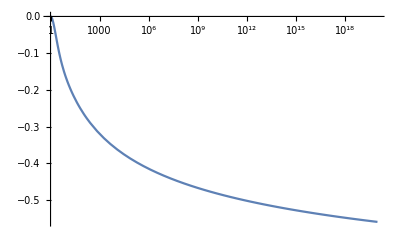

```mathematica
Δ = ((9/4)trh[3] -(6/4)trh[1]trh[2] + (1/4) trh[1]^3)/(((9/4)trh[4] -(6/4)trh[1]trh[3] + (1/4) trh[1]^4)^(3/4))-1;
LogLinearPlot[Δ, {κ, 1, 10^20}]
```

```mathematica
Wick's contractions
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Finds all distinct Wick's contraction pairs and their occurences
```

```mathematica
ArePairs[A_] :=  AllTrue[A, Length[#] ==2 &];

EvalTerm[list_]:=(
For[count = 0; i=1, i< 1+Length[list], i=i+1, If[list[[i,1]] == list[[i,2]], count=count+1, count = count]];
dpower = If[count==Length[list], count, count+1];
d^dpower
)

indices = {a[1], a[2], a[3], a[4], b[1], b[2]};
partitions = SetPartitions[indices];
all = Select[partitions, ArePairs];
graph = all[[1]]
cycle = {graph[[1]]};
link = graph[[1]]
step[cycle_, link_]:=(

)
(*
val =Table[EvalTerm[distinct[[i]]] , {i, Length[distinct]}] ;
num = Table[Count[all, distinct[[i]]], {i, Length[distinct]}] ;
Table[{distinct[[i]], Count[all, distinct[[i]]]} , {i, Length[distinct]}] //Column
*)
```

{{a[1],a[2]},{a[3],a[4]},{b[1],b[2]}}

```mathematica
(d+2)(d+4)(d+6) //Expand
```

48+44 d+12 d^2+d^3

```mathematica
list = {{1,1},{2,2},{3,4},{3,4}};


EvalTerm[list]
```

d^3

```mathematica
Vol = 2 π^(d/2)/Gamma[d/2];
Integrate[ r^n r^(d-1)Vol Exp[-r^2/2]/(2π)^(d/2), {r, 0, ∞}] //Simplify
```

ConditionalExpression[(2^(n/2) Gamma[(d+n)/2])/Gamma[d/2], Re[d+n]>0]

### Ratio: d Tr[H]^2 / Tr[H^2]

```mathematica
frac= 1/(d Tanh[ k /(2d)]Coth[k/2]);
Asymptotic[frac, d-> ∞]
```

(2 Tanh[k/2])/k

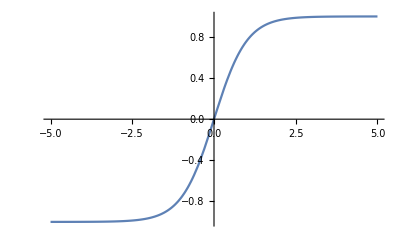

x-x^3/3+(2 x^5)/15+O[x]^6

```mathematica
Plot[Tanh[x],{x, -5, 5}]
Series[Tanh[x], {x, 0, 5}]
```

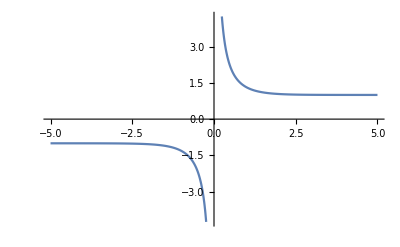

1/x+x/3-x^3/45+(2 x^5)/945+O[x]^6

```mathematica
Plot[Coth[x],{x, -5, 5}]
Series[Coth[x], {x, 0, 5}]
```

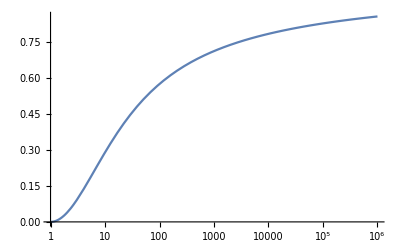

x^2/12-x^4/120+O[x]^5

0.289336

0.574305

0.711049

0.782896

0.826286

0.855235

```mathematica
Δ = 1 - Tanh[Log[κ]/2]/(Log[κ]/2 );
LogLinearPlot[Δ, {κ, 1, 10^6}]
Series[1 - Tanh[x/2]/(x/2 ), {x, 0, 4}]
N[Δ /. {κ-> 10}]
N[Δ /. {κ-> 100}]
N[Δ /. {κ-> 1000}]
N[Δ /. {κ-> 10000}]
N[Δ /. {κ-> 100000}]
N[Δ /. {κ-> 1000000}]
```